# Spherical Brane-Skyrmions: Shooting Method

Author: Sergio Sánchez Rentero
Contact: sergis15@ucm.es
Links: https://github.com/sergiosr150703-lang 

Project Context: This code is part of a Master’s Thesis in Theoretical Physics. The project investigates the canonical quantization of topological solitons in brane-world scenarios. In particular, this notebook takes care about computing the profile of classical Brane-Skyrmions through minimizing their energy functional. We first compute the corresponding equations of motion, and then we solve them with a Shooting method.

Last Updated: June 2026

## Equations of Motion

```mathematica
Clear["Global`*"];
Needs["VariationalMethods`"]; (*Useful library*)

(*Definition of necessary functions*)
ρ[r_] := Sqrt[r^2+β*Sin[F[r]]^2];
A[r_] := (1+β*F'[r]^2)/(ρ'[r]^2);
R[r_] = FullSimplify[-(2/ρ[r]^2)*(1 - 1/A[r]) - (2*A'[r])/(ρ[r]*ρ'[r]*A[r]^2)];
(*Lagrangian*)
L=FullSimplify[(1-*R[r])*Sqrt[1+β*F'[r]^2]*ρ[r]^2]
```

(r^2+β Sin[F[r]]^2) √(1+β F'[r]^2) (1-1/(4 (r^2+β Sin[F[r]]^2)^2 (1+β F'[r]^2)^2)β λ (8 Sin[F[r]]^2+F'[r] (-8 r Sin[2 F[r]]+F'[r] (-8 r^2-5 β+8 (2 r^2+β) Cos[2 F[r]]-3 β Cos[4 F[r]]+β F'[r] (-8 r Sin[2 F[r]]+(-8 r^2-9 β+4 (4 r^2+3 β) Cos[2 F[r]]-3 β Cos[4 F[r]]) F'[r])))-4 (2 r^2+β-β Cos[2 F[r]]) (-Sin[2 F[r]]+2 r F'[r]) F''[r]))

```mathematica
(*Calculation of Euler-Lagrangian equations via Variational Methods*)
Equation=EulerEquations[L,F[r],r];

(*Raw results*)
Print["Euler-Lagrange equation:"];
Style[TraditionalForm[Equation]]
```

Euler-Lagrange equation:

1/(64 (β (F'(r))^2+1)^(5/2) (β sin^2(F(r))+r^2)^3)β (β-β cos(2 F(r))+2 r^2) (-2 F''(r) (β-β cos(2 F(r))+2 r^2) (3 β^2+12 β λ-4 β cos(2 F(r)) (β+2 λ+2 r^2)+β (β-4 λ) cos(4 F(r))+8 r^4+8 β r^2)-8 β^2 r (F'(r))^5 (3 β^2+6 β λ-4 (β+2 λ) (β+2 r^2) cos(2 F(r))+β (β+2 λ) cos(4 F(r))+8 r^4+8 β r^2)-16 β r (F'(r))^3 (3 β^2-3 β λ-4 cos(2 F(r)) (β^2+2 r^2 (β+λ))+β (β+3 λ) cos(4 F(r))+8 r^4+8 β r^2)+4 β^2 (F'(r))^4 sin(2 F(r)) (3 β^2+6 β λ-4 (β+2 λ) (β+2 r^2) cos(2 F(r))+β (β+2 λ) cos(4 F(r))+8 r^4+8 β r^2-32 λ r^2)+β (F'(r))^2 (8 sin(2 F(r)) (3 β^2-β λ-4 cos(2 F(r)) (β^2+2 r^2 (β+λ))+β (β+λ) cos(4 F(r))+8 r^4+8 β r^2-16 λ r^2)-2 F''(r) (β-β cos(2 F(r))+2 r^2) (3 β^2+6 β λ-4 β cos(2 F(r)) (β+2 λ+2 r^2)+β (β+2 λ) cos(4 F(r))+8 r^4+8 β r^2+48 λ r^2))-8 r F'(r) (3 β^2-12 β λ+12 β λ F''(r) sin(2 F(r)) (-β+β cos(2 F(r))-2 r^2)-4 β cos(2 F(r)) (β-2 λ+2 r^2)+β^2 cos(4 F(r))+4 β λ cos(4 F(r))+8 r^4+8 β r^2)+4 sin(2 F(r)) (3 β^2-8 β λ-4 β cos(2 F(r)) (β-2 λ+2 r^2)+β^2 cos(4 F(r))+8 r^4+8 β r^2))==0

```mathematica
(*Simplification of the results*)
EqFinal=FullSimplify[Equation,Assumptions->{r>0,β>0}];
Print["Simplified equation:"];
Style[TraditionalForm[EqFinal]]
```

Simplified equation:

1/(2 (β (F'(r))^2+1)^(5/2) (β sin^2(F(r))+r^2))(β-β cos(2 F(r))+2 r^2) (2 F''(r) (β-β cos(2 F(r))+2 r^2) (3 β (β+4 λ)-4 β cos(2 F(r)) (β+2 λ+2 r^2)+β (β-4 λ) cos(4 F(r))+8 r^4+8 β r^2)+8 β^2 r (F'(r))^5 (3 β (β+2 λ)+(β+2 λ) (β cos(4 F(r))-4 (β+2 r^2) cos(2 F(r)))+8 r^4+8 β r^2)+16 β r (F'(r))^3 (3 β (β-λ)-4 cos(2 F(r)) (β^2+2 r^2 (β+λ))+β (β+3 λ) cos(4 F(r))+8 r^4+8 β r^2)-4 β^2 (F'(r))^4 sin(2 F(r)) (3 β (β+2 λ)+(β+2 λ) (β cos(4 F(r))-4 (β+2 r^2) cos(2 F(r)))+8 r^4+8 r^2 (β-4 λ))-β (F'(r))^2 (8 sin(2 F(r)) (β (3 β-λ)-4 cos(2 F(r)) (β^2+2 r^2 (β+λ))+β (β+λ) cos(4 F(r))+8 r^4+8 r^2 (β-2 λ))-2 F''(r) (β-β cos(2 F(r))+2 r^2) (3 β (β+2 λ)-4 β cos(2 F(r)) (β+2 λ+2 r^2)+β (β+2 λ) cos(4 F(r))+8 r^4+8 r^2 (β+6 λ)))+8 r F'(r) (3 β (β-4 λ)-12 β λ F''(r) sin(2 F(r)) (β-β cos(2 F(r))+2 r^2)-4 β cos(2 F(r)) (β-2 λ+2 r^2)+β (β+4 λ) cos(4 F(r))+8 r^4+8 β r^2)-4 sin(2 F(r)) (3 β^2-8 β λ-4 β cos(2 F(r)) (β-2 λ+2 r^2)+β^2 cos(4 F(r))+8 r^4+8 β r^2))==0

```mathematica
(*Isolate F''*)
Print["\nIsolating derivative of higher order (F''):"];
IsolatedSol= FullSimplify[Solve[EqFinal,F''[r]]][[1]][[1]][[2]];
Print[Style[TraditionalForm[IsolatedSol]]];
```

Isolating derivative of higher order (F''):

(2 (β (F'(r))^2+1) (sin(2 F(r))-2 r F'(r)) (3 β^2-8 β λ+β F'(r) (F'(r) (3 β (β+2 λ)+(β+2 λ) (β cos(4 F(r))-4 (β+2 r^2) cos(2 F(r)))+8 r^4+8 β r^2)+16 λ r sin(2 F(r)))-4 β cos(2 F(r)) (β-2 λ+2 r^2)+β^2 cos(4 F(r))+8 r^4+8 β r^2))/((β-β cos(2 F(r))+2 r^2) (3 β (β+4 λ)+β F'(r) (F'(r) (3 β (β+2 λ)-4 β cos(2 F(r)) (β+2 λ+2 r^2)+β (β+2 λ) cos(4 F(r))+8 r^4+8 r^2 (β+6 λ))-48 λ r sin(2 F(r)))-4 β cos(2 F(r)) (β+2 λ+2 r^2)+β (β-4 λ) cos(4 F(r))+8 r^4+8 β r^2))

## Numerical solution: Shooting method

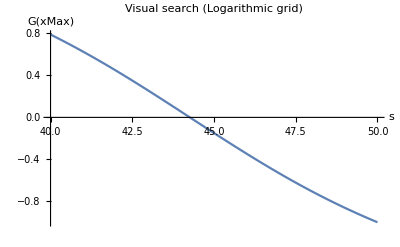

```mathematica
Clear[s,r,x,G,β,λ];

lam=1/10; (*Coupling*)
rMin=10^-5; (*Lowest integration limit*)
rMax=25; (*Highest integration*)

(*We define a logarithmic grid*)
xMin=Log[rMin];
xMax=Log[rMax];
(*Equation of motion*)
Shoot=FullSimplify[IsolatedSol/. λ->lam/. β->1];

(*Logarithmic variable change*)
ShootX=Shoot/. {r->Exp[x],F[r]->G[x],F'[r]->Exp[-x]*G'[x]};
(*New equation F''=Shoot transforms in:*)
(*Exp[-2x]*(G''-G')=ShootX==>G''=G'+Exp[2x]*ShootX*)
EqLog=G''[x]==G'[x]+Exp[2x]*ShootX;

(*Initial conditions with variable x*)
(*F(r)=Pi-s*r==>G(x)=Pi-s*Exp[x]*)
PosCondition=G[xMin]==Pi-s*Exp[xMin];
VelCondition=G'[xMin]==-s*Exp[xMin];
(*Solver paramétrico en función de s*)
ParametricSol=ParametricNDSolveValue[{EqLog,PosCondition,VelCondition},G,{x,xMin,xMax},{s},Method->"StiffnessSwitching",MaxSteps->500000,WorkingPrecision->30 (*We don't want the solution to explode in the origin*)];

(*Visual search of s*)
Plot[ParametricSol[s][xMax],{s,40,50},AxesLabel->{"s","G(xMax)"},PlotLabel->"Visual search (Logarithmic grid)",PlotRange->All]
```

Initial slope found: s = 44.2618040600454175297410946736

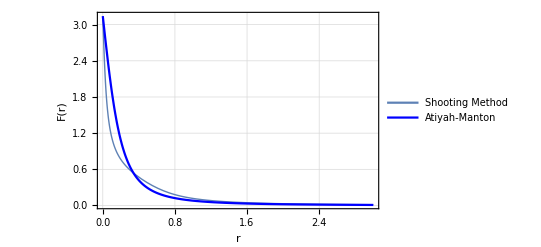

Export completed.

```mathematica
(*Exact calculation of s*)
Sol=FindRoot[ParametricSol[s][xMax]==0,{s,44,45},WorkingPrecision->30,AccuracyGoal->10,PrecisionGoal->10];
Slope=s/. Sol;
Print["Initial slope found: s = ",Slope];

FinalProfile=ParametricSol[Slope]; (*Final profile*)
Manton[r_]=Pi*(1-r/Sqrt[r^2+(0.23)^2]); (*Atiyah-Manton profile*)

(*Graphics*)
Plot[{FinalProfile[Log[r]],Manton[r]},{r,rMin,3},PlotRange->All,Frame->True,FrameLabel->{Style["r",12,Italic,Black],Style["F(r)",12,Italic,Black]},PlotLegends->Placed[{"Shooting Method","Atiyah-Manton"},{0.8,0.8}],GridLines->Automatic,PlotStyle->{Thick,Blue}]

(*Export of the solution*)
SetDirectory[NotebookDirectory[]];
ExportPoints=N[Table[{Exp[x],FinalProfile[x]},{x,xMin,xMax,(xMax-xMin)/25000}]];
Export["Profile_Shooting_Lambda_01.csv",ExportPoints];
Print["Export completed."];
```

```mathematica
(*Undo the logarithmic change*)
FShoot[r_]:=FinalProfile[Log[r]];

(*Energy calculation with variable r*)
EnergyDensity=(L/. {λ->lam,β->1})-r^2;
Integrand[r_]:=EnergyDensity/. {F[r]->FShoot[r],F'[r]->FShoot'[r],F''[r]->FShoot''[r]};
TotalEnergy=(4*Pi/(2*Pi^2))*NIntegrate[Integrand[r],{r,rMin,rMax},Method->"LocalAdaptive"];
Print["E = ",TotalEnergy];
```

E = 1.42282

## Cross Check del Shooting Method

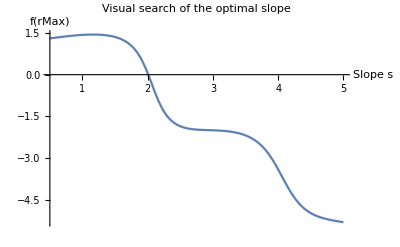

Initial slope found: s = 2.00844

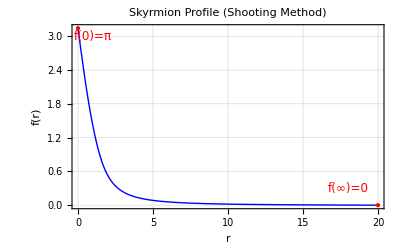

```mathematica
(*This part is to check that the Shooting method of above can solve the known profile of classical Skyrmions. See Fig 9.1 of Topological solitons, N.S.Manton and P.Sutcliffe.*)

Clear[s,r]
(*Skyrmion equation of motion*)
EoM=(r^2+2*Sin[f[r]]^2)*f''[r]+2*r*f'[r]+Sin[2*f[r]]*(f'[r]^2-1-Sin[f[r]]^2/r^2)==0;

rMin=10^-4;
rMax=20; 
ParametricSol=ParametricNDSolveValue[{EoM,f[rMin]==Pi-s*rMin,f'[rMin]==-s},f,{r,rMin,rMax},{s}];

(*Optimal slope search*)
Plot[ParametricSol[s][rMax],{s,0.5,5},AxesLabel->{"Slope s","f(rMax)"}, PlotLabel->"Visual search of the optimal slope"]
Sol=FindRoot[ParametricSol[s][rMax]==0, {s,2.0}];
Slope=s/. Sol;

Print["Initial slope found: s = ",Slope];

(*Final plot*)
FinalProfile=ParametricSol[Slope];

Plot[FinalProfile[r],{r,rMin,rMax},PlotRange->All,Frame->True,FrameLabel->{Style["r",12,Italic,Black],Style["f(r)",12,Italic,Black]},PlotLabel->Style["Skyrmion Profile (Shooting Method)",14,Black],GridLines->Automatic,PlotStyle->{Thick,Blue},Epilog->{PointSize[Medium],Red,Point[{0,Pi}],Inset[Style["f(0)=π",12,Red],{1,3}],Red,Point[{rMax,0}],Inset[Style["f(∞)=0",12,Red],{rMax-2,0.3}]}]
```